## Preamble

```mathematica
SetDirectory@NotebookDirectory[]

trapvs=Import["./trap-verts.csv", "CSV"];
trapvs⟦;;,2;;⟧=StringTrim/@trapvs⟦;;,2;;⟧; 
labels = trapvs⟦;;,2⟧;

n =Length@trapvs
inputs = Table[IntegerDigits[inp, 2,n],{inp,0, 2^n-1 }];
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/socsim

17

### Deselect Input Cases with War Node Preset to Active State

```mathematica
spaceSz = 2^n-1;
inpRange = Range[0,spaceSz];
validInpsB=Table[
IntegerDigits[inp, 2,n],
{inp,inpRange}
];
Dimensions@validInpsB
validIdx = Select[inpRange+1,(validInpsB⟦#,-1⟧≠1 )&];
validIdx//Length
```

{131072,17}

65536

```mathematica
Union[validInpsB⟦validIdx, -1⟧]
```

{0}

```mathematica
Union@@validInpsB
```

{0,1}

```mathematica
IntegerDigits[2^17, 2, 17]
IntegerDigits[2^17-1, 2, 17]
IntegerDigits[2^16-1, 2, 18]
ConstantArray[1, 17]
FromDigits[%,2]
IntegerDigits[%, 2, 17]
Log[2,%%+1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

131071

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

17

## Analysing Exhaustive Search Results

### Heaviside Activation Fxn

{2,65536}

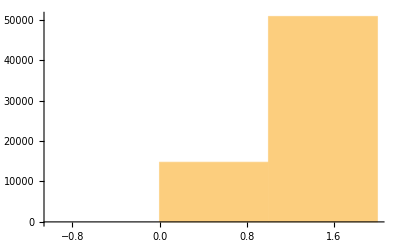
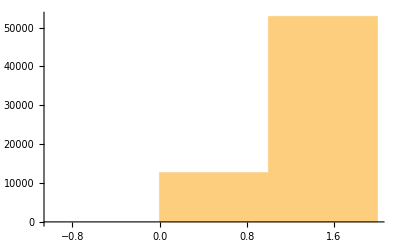

{{1,1,1},{1,1,1}}

```mathematica
stepres = (Transpose@Import["dyn-stat-cmp-step.csv"])⟦;;,validIdx⟧;
Dimensions@stepres
Histogram/@stepres
Quartiles/@stepres
```

#### Dyn - Stat Divergence

2076

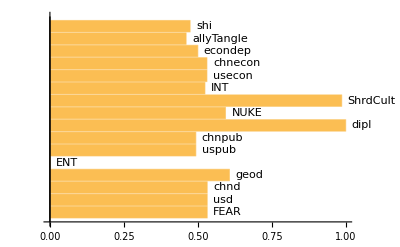

{dipl,ShrdCult}

```mathematica
divs = Cases[
Range@Length@stepres⟦1⟧,
i_/;(Subtract@@(stepres⟦;;,i⟧)≠0)
];
Length@divs
divmasks = (validInpsB⟦validIdx⟦#⟧⟧&/@divs);
divmeas = Mean@divmasks;
(*ListLinePlot[divmeas, PlotRange->All,Mesh->All]*)
BarChart[divmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]

labels⟦Select[Range@n, (Abs[divmeas⟦#⟧-Max[divmeas]]<0.05)&]⟧
```

#### War and Peace ...

12672

Pct of Peace-vs-War Convergences:19.3359

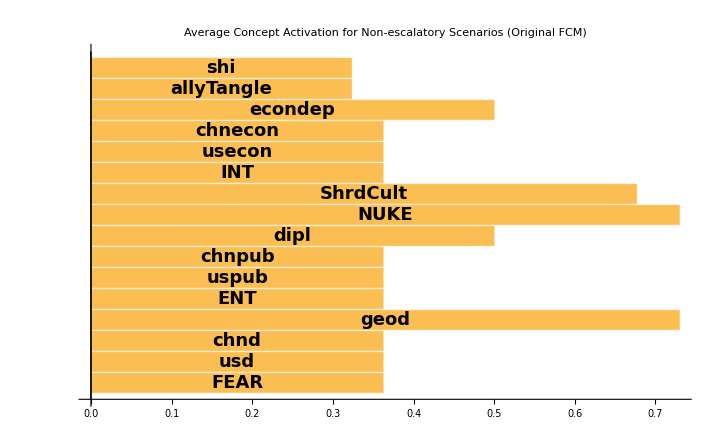

```mathematica
nowars = Cases[
Range@Length@stepres⟦2⟧,
i_/;stepres⟦2,i⟧==0
];(*//Length*)
Length@nowars
nwstates = (validInpsB⟦validIdx⟦#⟧⟧&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@stepres⟦2⟧)//N]

nwmeas = Mean@nwstates;
(*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios\n(Original FCM)", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

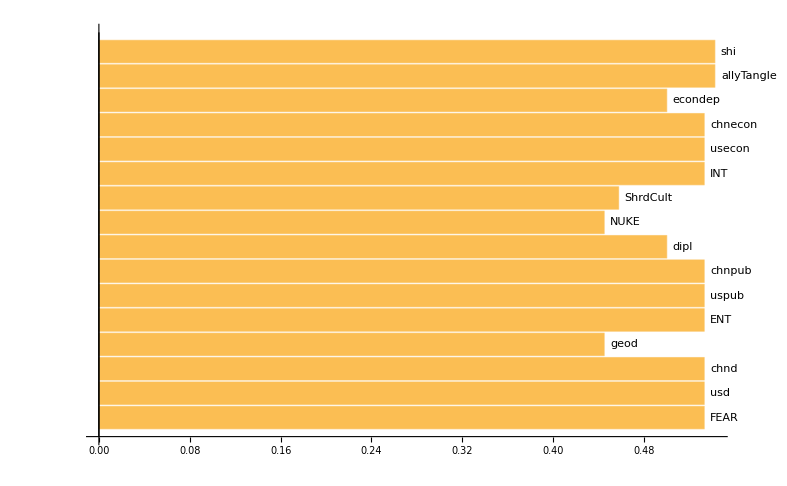

```mathematica
mTh=Mean@stepres⟦2⟧;
wars = Cases[
Range@Length@stepres⟦2⟧,
i_/;stepres⟦2,i⟧>mTh
];
wstates = (validInpsB⟦validIdx⟦#⟧⟧&/@wars);

wmeas = Mean@wstates;
BarChart[wmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

### Linear Activation Fxn

{2,65536}

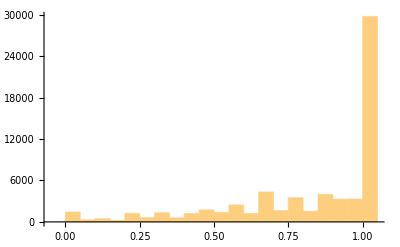
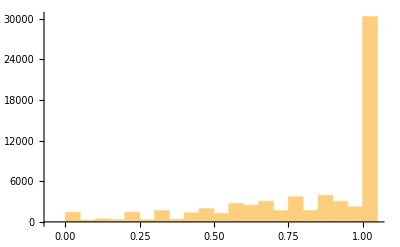

{{0.68604,0.966667,1.},{0.666667,0.944444,1.}}

```mathematica
linres = (Transpose@Import["dyn-stat-cmp-linear.csv"])⟦;;,validIdx⟧;
Dimensions@linres
Histogram/@linres
Quartiles/@linres
```

#### Dyn - Stat Divergence

28296

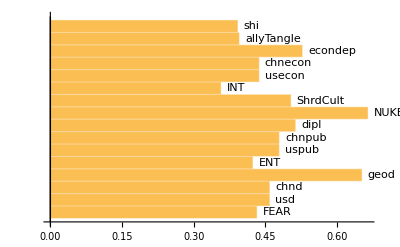

```mathematica
divs = Cases[
Range@Length@linres⟦1⟧,
i_/;(Subtract@@(linres⟦;;,i⟧)≠0)
];
Length@divs
divmasks = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@divs);
divmeas = Mean@divmasks;
BarChart[divmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

#### War and Peace ...

Pct of Peace-vs-War Convergences:14.5874

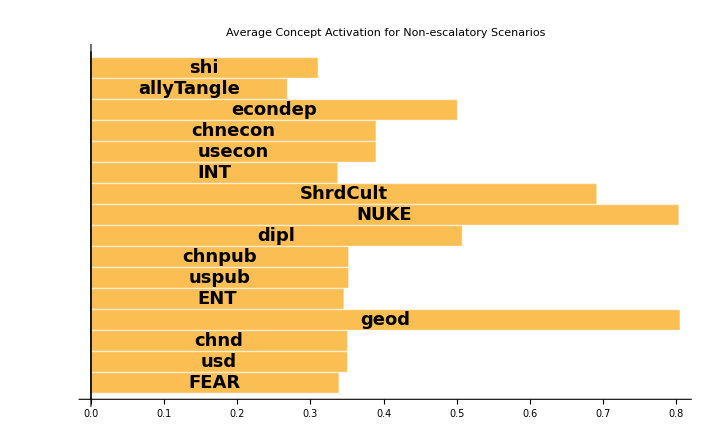

```mathematica
nowars = Cases[
Range@Length@linres⟦2⟧,
i_/;linres⟦2,i⟧≤0.5
];
nwstates = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@linres⟦2⟧)//N]

nwmeas = Mean@nwstates;
(*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

### Logistic Activation Fxn

{2,65536}

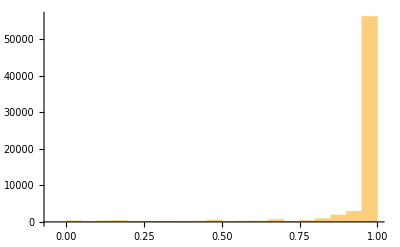
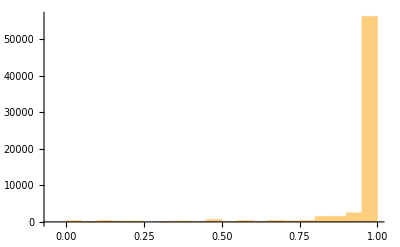

{{0.974075,0.993299,0.997912},{0.974026,0.993327,0.997915}}

```mathematica
logres=(Transpose@Import["dyn-stat-cmp-logit.csv"])⟦;;,validIdx⟧;
Dimensions@logres
Histogram/@logres
Quartiles/@logres
```

#### Dyn - Stat Divergence

60488

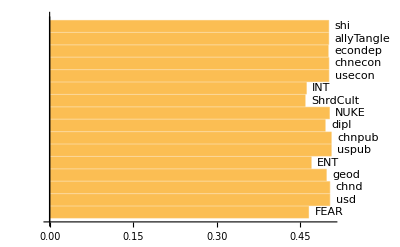

```mathematica
divs = Cases[
Range@Length@logres⟦1⟧,
i_/;(Subtract@@(logres⟦;;,i⟧)≠0)
];
Length@divs
divmasks = (validInpsB⟦validIdx⟦#⟧⟧&/@divs);
(*divmasks = (IntegerDigits[validIdx⟦#⟧, 2,n]&/@divs);*)
divmeas = Mean@divmasks;
(*ListLinePlot[divmeas, PlotRange->All,Mesh->All]*)
BarChart[divmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```

#### War and Peace ...

Pct of Peace-vs-War Convergences:3.36609

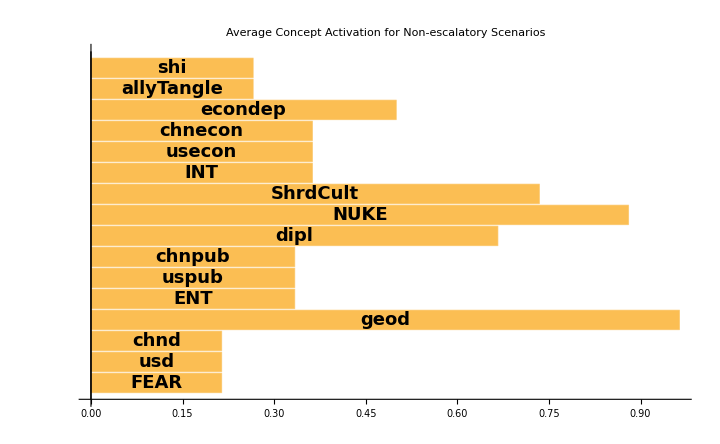

```mathematica
nowars = Cases[
Range@Length@logres⟦2⟧,
i_/;logres⟦2,i⟧≤0.50
];(*//Length*)
nwstates = (validInpsB⟦validIdx⟦#⟧⟧&/@nowars);

Print["Pct of Peace-vs-War Convergences:",100×Length[nowars]/(Length@logres⟦2⟧)//N]
nwmeas = Mean@nwstates; (*labels⟦Select[Range[n-1], (nwmeas⟦#⟧>0.45)&]⟧*)
BarChart[nwmeas⟦;;-2⟧,
ChartLabels->Placed[(Style[#, Bold, 18]&/@labels),Center],
BarOrigin->Left,
PlotLabel->Style["Average Concept Activation for Non-escalatory Scenarios", Bold, 24],
PlotRange->All,
ImageSize->72×10
]
```

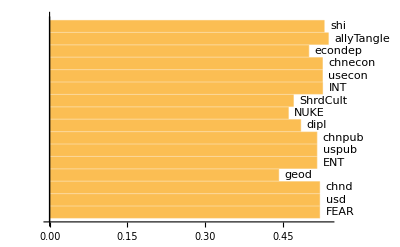

```mathematica
mTh=Mean@logres⟦2⟧;
wars = Cases[
Range@Length@logres⟦2⟧,
i_/;logres⟦2,i⟧>mTh
];
wstates = (validInpsB⟦validIdx⟦#⟧⟧&/@wars);

wmeas = Mean@wstates;
BarChart[wmeas⟦;;-2⟧,
ChartLabels->Placed[labels,After],
BarOrigin->Left,
 PlotRange->All]
```